```mathematica
(* List of fast Deleglise-Rivat alpha factors for x ≤ 10^21 found by running pi(x) benchmarks using the find_fastest_alpha.sh script *)

alphaDelegliseRivat =  { (* {x, alpha} *) {1, 1}, {10^1, 1}, {10^2, 1},{10^3, 1},{10^4, 1},{10^5, 1},{10^6,1.172}, {10^7,1.561},{10^8,2.278},{10^9,3.455},{10^10,4.125},{10^11,5.195}, {10^12,6.960}, {10^13, 8.272},  {10^14, 11.462}, {10^15,  15.619}, {10^16, 18.980}, {10^17, 24.119}, {10^18,29.115}, {10^19,34.635},{10^20, 42.072},{10^21,49.575}}
```

{{1,1},{10,1},{100,1},{1000,1},{10000,1},{100000,1},{1000000,1.172},{10000000,1.561},{100000000,2.278},{1000000000,3.455},{10000000000,4.125},{100000000000,5.195},{1000000000000,6.96},{10000000000000,8.272},{100000000000000,11.462},{1000000000000000,15.619},{10000000000000000,18.98},{100000000000000000,24.119},{1000000000000000000,29.115},{10000000000000000000,34.635},{100000000000000000000,42.072},{1000000000000000000000,49.575}}

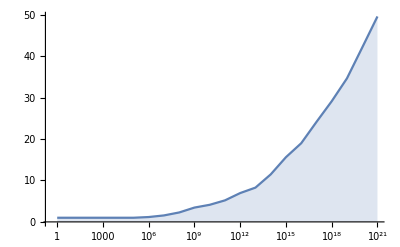

```mathematica
ListLogLinearPlot[alphaDelegliseRivat,Filling->Bottom, Joined-> True]
```

```mathematica
(* alpha is a tuning factor that balances the compuation of the easy special leaves and the hard special leaves. The formula below is used in the file src/primecount.cpp to calculate a fast alpha factor for the computation of pi(x). *)

NonlinearModelFit[alphaDelegliseRivat, a(Log[x])^3 + b (Log[x])^2 + c Log[x] + d, {a,b, c, d}, x]
```

FittedModel[0.802942+0.123034 Log[x]-0.0160586 Log[x]^2+0.000711339 Log[x]^3]

```mathematica
(* List of fast Deleglise-Rivat alpha factors for x greater than 10^21 found by running pi(x) benchmarks. A larger alpha reduces CPU cache misses for large pi(x) computations. *)

alphaDelegliseRivatLarge =  { (* {x, alpha} *) {1, 1}, {10^1, 1}, {10^2, 1},{10^3, 1},{10^4, 1},{10^5, 1},{10^6,1.172}, {10^7,1.861},{10^8,2.778},{10^10,5.426},{10^11,7.795}, {10^12,10.960}, {10^13, 15.22}, {10^16, 34.80}, {10^20, 79.68},{10^21,96.86},{10^22,109.61},{10^23,130.33},{10^24, 154.69}}
```

{{1,1},{10,1},{100,1},{1000,1},{10000,1},{100000,1},{1000000,1.172},{10000000,1.861},{100000000,2.778},{10000000000,5.426},{100000000000,7.795},{1000000000000,10.96},{10000000000000,15.22},{10000000000000000,34.8},{100000000000000000000,79.68},{1000000000000000000000,96.86},{10000000000000000000000,109.61},{100000000000000000000000,130.33},{1000000000000000000000000,154.69}}

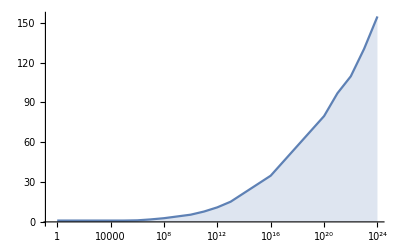

```mathematica
ListLogLinearPlot[alphaDelegliseRivatLarge,Filling->Bottom, Joined-> True]
```

```mathematica
(* alpha is a tuning factor that balances the compuation of the easy special leaves and the hard special leaves. The formula below is used in the file src/primecount.cpp to calculate a fast alpha factor for the computation of pi(x). *)

NonlinearModelFit[alphaDelegliseRivatLarge, a(Log[x])^3 + b (Log[x])^2 + c Log[x] + d, {a,b, c, d}, x]
```

FittedModel[0.591972+0.282139 Log[x]-0.0375705 Log[x]^2+0.00149066 Log[x]^3]

```mathematica
(* Below is another formula which is quite accurate for calculating the
 Deleglise-Rivat alpha factor in primecount. The constant 2200 has
 been obtained by running many pi(10^20) benchmarks. *)

alpha[x_] := (Log[x])^3 / (2200 (Log[Log[10^20]] / Log[Log[x]])^3)
```

```mathematica
(* List of fast Lagarias-Miller-Odlyzko alpha factors found by running pi(x) benchmarks. *)

alphaLMO = {(* {x, alpha} *) {1, 1},{10^10, 1.208}, {10^11, 1.281},  {10^12, 1.364},{10^13, 1.679},{10^14, 1.890},{10^15,2.011},{10^16, 2.113},{10^17, 2.359},{10^18, 2.556}}
```

{{1,1},{10000000000,1.208},{100000000000,1.281},{1000000000000,1.364},{10000000000000,1.679},{100000000000000,1.89},{1000000000000000,2.011},{10000000000000000,2.113},{100000000000000000,2.359},{1000000000000000000,2.556}}

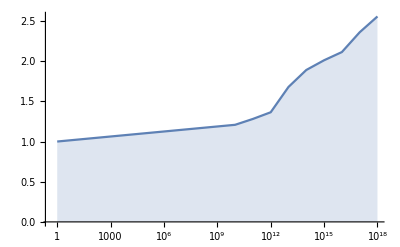

```mathematica
ListLogLinearPlot[alphaLMO,Filling->Bottom, Joined-> True]
```

```mathematica
(* alpha is a tuning factor that balances the compuation of the easy special leaves and the hard special leaves. The formula below is used in the file src/primecount.cpp to calculate a fast alpha factor for the computation of pi(x). *)
```

```mathematica
NonlinearModelFit[alphaLMO, a(Log[x])^2 + b  Log[x] + c, {a,b, c}, x]
```

FittedModel[0.990948-0.0261411 Log[x]+0.00156512 Log[x]^2]